Authors:  Jozef Hanč, Martina Hančová 
Faculty of Science, P. J. Šafárik University in Košice, Slovakia
email: martina.hancova@upjs.sk

## Analytical expression for f(z): MachinePrecision

-Graphics-

### Parameters

```mathematica
{a1,a2,b1, b2} ={0.5,8.5,1.0,93.0}
```

{0.5,8.5,1.,93.}

### Definitions

```mathematica
U[a_,b_, z_]:=HypergeometricU[a,b,z];
G[z_]:=Gamma[z];
```

```mathematica
{a,b} = {a1+a2, b1+b2};
c = b1^a1*b2^a2/b^(a-1);
{cp,cm} ={ c/G[a1], c/G[a2]};
```

```mathematica
f[z_]:=Piecewise[{
{cm*Exp[+z*b2] *U[1-a2, 2-a, -b*z],z < 0},
{cp*Exp[-z*b1]*U[1-a1,2-a, b*z],z>0},
{If[a>1,c*G[a-1]/G[a1]/G[a2],Infinity], z ==0} 
}]
```

### Test and Plots

```mathematica
f[0.25] //TraditionalForm
```

0.689707

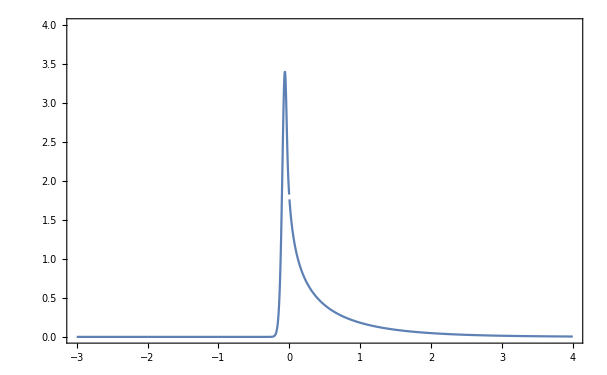

```mathematica
Plot[f[z], {z,-3,4}, PlotRange ->{0,4}, Frame->True]
```

## Results - CSV file

```mathematica
$VersionNumber
```

12.3

```mathematica
$OutputSizeLimit=100
```

100

```mathematica
n = 10000-1;
```

```mathematica
dataset =Flatten[RepeatedTiming[Table[f[x], {x, -3.0, 4.0, 7.0/n}]]]
```

{2.17662,1.03379×10^-106,1.10141×10^-106,1.17345×10^-106,1.25021×10^-106,1.33198×10^-106,1.4191×10^-106,1.51192×10^-106,1.61082×10^-106,1.71617×10^-106,1.82842×10^-106,9979,0.00470222,0.00469853,0.00469484,0.00469115,0.00468746,0.00468378,0.0046801,0.00467643,0.00467275,0.00466908,0.00466542}
 |  |  |  |

```mathematica
FileName = StringJoin["Wolfram53bit",ToString[n+1],".txt"];
```

```mathematica
Export[FileName, dataset, "CSV"]
```

Wolfram53bit10000.txt

```mathematica
SystemOpen[FileName]
```

### Export file on the cloud

```mathematica
CopyFile[FileName,CloudObject[FileName],OverwriteTarget->True]
```

CloudObject[https://www.wolframcloud.com/obj/hancjozef/Wolfram53bit10000.txt]
 |  |  |  |

```mathematica
$MachinePrecision
```

15.9546

## References

This notebook belongs to supplementary materials of the paper submitted to Journal of Statistical Computation and
Simulation and available at  https://arxiv.org/abs/2105.04427.

Hančová, M., Gajdoš, A., Hanč, J. (2021). A practical, effective calculation of gamma difference distributions with open data science tools.
arXiv:2105.04427 [cs, math, stat], https://arxiv.org/abs/2105.04427

Abstract
 At present, there is still no officially accepted and extensively verified implementation of computing the gamma difference distribution allowing unequal shape parameters. We explore four computational ways of the gamma difference distribution with the different shape parameters resulting from time series kriging, a forecasting approach based on the best linear unbiased prediction, and linear mixed models. The results of our numerical study, with emphasis on using open data science tools, demonstrate that our open tool implemented in high-performance Python(with Numba) is exponentially fast, highly accurate, and very reliable. It combines numerical inversion of the characteristic function and the trapezoidal rule with the double exponential oscillatory transformation (DE quadrature). At the double 53-bit precision, our tool outperformed the speed of the analytical 
computation based on Tricomi’s U(a, b, z) function in CAS software (commercial Mathematica, open SageMath) by 1.5-2 orders. At the precision of scientific numerical computational tools, it exceeded open SciPy, NumPy, and commercial MATLAB 5-10 times. The potential future application of our tool for a mixture of characteristic functions could open new possibilities for fast data analysis based on exact probability distributions in areas like multidimensional statistics, measurement uncertainty analysis in metrology as well as in financial mathematics and risk analysis.